```mathematica
R = {{-r3-k1, k1, r3},{r1, -r1-k2, k2},{0, 0,0}}
```

{{-k1-r3,k1,r3},{r1,-k2-r1,k2},{0,0,0}}

```mathematica
Q = Eigenvectors[R]
```

{{1,1,1},{-(k1-k2-r1+r3+√(k1^2-2 k1 k2+k2^2+2 k1 r1+2 k2 r1+r1^2+2 k1 r3-2 k2 r3-2 r1 r3+r3^2))/(2 r1),1,0},{-(k1-k2-r1+r3-√(k1^2-2 k1 k2+k2^2+2 k1 r1+2 k2 r1+r1^2+2 k1 r3-2 k2 r3-2 r1 r3+r3^2))/(2 r1),1,0}}

```mathematica
A= Eigenvalues[R]
```

{0,1/2 (-k1-k2-r1-r3-√((k1+k2+r1+r3)^2-4 (k1 k2+k2 r3+r1 r3))),1/2 (-k1-k2-r1-r3+√((k1+k2+r1+r3)^2-4 (k1 k2+k2 r3+r1 r3)))}

```mathematica
P = MatrixExp[R*t];
```

```mathematica
p23 = FullSimplify[P[[2,3]] /.{r1->1,r3->100,k1->1,k2->1}]
```

1-(ⅇ^(-103 t/2) (9805 Cosh[(√9805 t)/2]+101 √9805 Sinh[(√9805 t)/2]))/9805

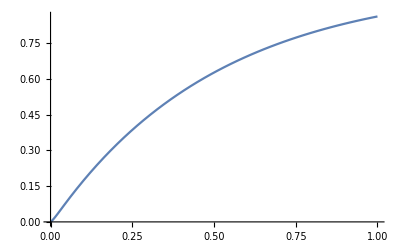

```mathematica
Plot[p23,{t,0,1}]
```

```mathematica
p32 = FullSimplify[P[[1,3]] /.{r1->1,r3->100,k1->1,k2->100}]
```

1-ⅇ^(-100 t)

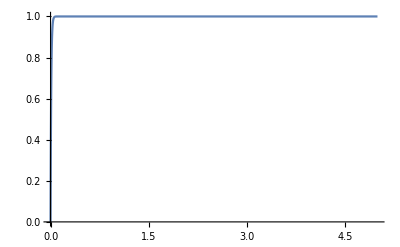

```mathematica
Plot[p32,{t,0,5}]
```

```mathematica
RR = {{-r4-k1, k1, 0,r4},{r1, -r1-k2, k2,0},{0,r2,-r2-k3,k3},{0, 0,0,0}}
```

{{-k1-r4,k1,0,r4},{r1,-k2-r1,k2,0},{0,r2,-k3-r2,k3},{0,0,0,0}}

```mathematica
ass={ t>0,k1>0, k2>0, k3 >0 , r1>0, r2>0,r4>0};
```

```mathematica
val = {k1-> 1, k2-> 1, k3 -> 1 , r1-> 1, r2-> 10,r4->1};
```

```mathematica
MatrixForm[RR]
```

```mathematica
RR[[3,4]]
```

k3

```mathematica
Meh = MatrixExp[RR*t];
```

```mathematica
Meh[[3,4]]
```

```mathematica
p34 = N[Meh[[3,4]] ]
```

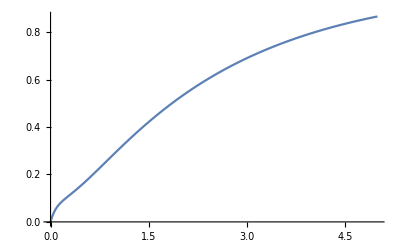

```mathematica
Plot[p34,{t,0,5}]
```

```mathematica
MehSimp = Meh /. ass;
```

```mathematica
Meh[[3,4]]
```

1/4 (-2-2 √2-2 (-2-√2)+(-2-√2) (-2+√2))+1/4 (2-2 √2-√2 (-2+√2)) ⅇ^(-2 t)+(2 ⅇ^((-2-√2) t))/(4+20 (-2-√2)+18 (-2-√2)^2+4 (-2-√2)^3)+(2 ⅇ^((-2+√2) t))/(4+20 (-2+√2)+18 (-2+√2)^2+4 (-2+√2)^3)

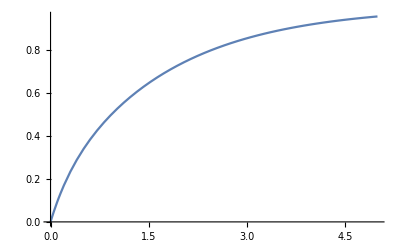

```mathematica
Plot[Meh[[3,4]],{t,0,5}]
```

```mathematica
blah = ((k1/(r1+k2)) + r4 / (r3+k4)) / (r4+k1 - ((k1r1)/(r1+k2)) - ((k4r4)/(r3+k4)))
```

(k1/(k2+r1)+r4/(k4+r3))/(k1-k1r1/(k2+r1)-k4r4/(k4+r3)+r4)

```mathematica
FullSimplify[blah]
```

(k1 (k4+r3)+(k2+r1) r4)/(-k1r1 (k4+r3)+(k2+r1) (-k4r4+(k4+r3) (k1+r4)))